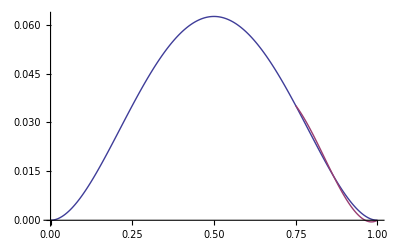

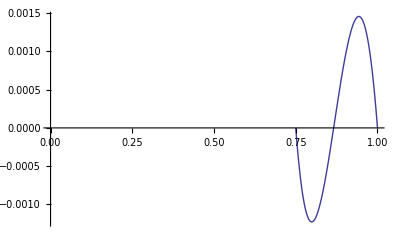

```mathematica
(*
   Проект по Числен Анализ 
  Ралица Димитрова, КН, 3-ти курс, адм. гр.1, ф.н. 80226
*)

(*
   Програмата пресмята естествения кубичен сплайн, интерполиращ функцията f(t) = sin(πt) / (1 - t + t^2) 
в интервала [0,1] във възлите Subscript[x, k]= k/n, k = 0, ..., n. 
 За целта се извежда система линейни уравнения, които удовлетворяват числата Subscript[{Subscript[d, k]}^n, k=0], зададени
 посредством Subscript[d, k] = Subscript[p, k]'(Subscript[x, k]), където Subscript[p, k](t) = Subscript[S, n](f;t)_(|t∈[Subscript[x, k], Subscript[x, k+1]]), k = 0,,1,...,n-1. 
 Системата се решава по метода на прогонката.
*)

(*
 Функцията f(t), за която се търси естествен кубичен сплайн, начална стойност на n, и степента на сплайна r
(в случая r=3, тъй като търсим кубичен сплайн)
*)
(*F[t_] := Sin[Pi*t]/(1-t+t^2)*)
F[t_] := t^2*((1-t)^2);
n= 3; 
r = 3;

(*
 Интерполационните възли, в които сплайна интерполира f(t) и разстоянието между всеки два възела 
(в случая то е едно и също, тъй като имаме равно отдалечени възли)
*)
Do[x[k] = k/(n+1), {k, 0, n+1}];
delta = 1/(n+1);

(*
  Реализация на метода на прогонката (в прав ход). a-тата, b-тата и c-тата са съответните коефициенти
пред търсените Subscript[{Subscript[d, k]}^n, k=1]
*)
Do[a[i] = 1, {i, 2, n}];

b[1] = 7/2;
b[n] = 7/2; 
Do[ b[i] = 4,{i, 2, n-1}];

Do[c[i] = 1, {i, 1, n-1}];

e[1] = 3*(2*F[x[2]] - F[x[1]] - F[x[0]])/(2*delta);
e[n] = 3*(F[x[n+1]] + F[x[n]] - 2*F[x[n-1]])/(2*delta);
Do[e[i] = 3*(F[x[i+1]] - F[x[i-1]])/delta, {i, 2, n-1}];

alfa[1] = -c[1]/b[1];
Do[alfa[k] = c[k]/(a[k]*alfa[k-1] + b[k]),{k, 2, n-1}];

beta[1] = e[1]/b[1];
Do[beta[k] = (e[k] - a[k]*beta[k-1])/(a[k]*alfa[k-1] + b[k]),{k, 2, n-1}];

(*
 задаване на търсените Subscript[{Subscript[d, k]}^n, k=1] и допълнителното условие за Subscript[d, 0] и Subscript[d, n+1]
*)
d[0] = 3*(F[x[1]] - F[x[0]])/2*delta - d[1]/2;
d[n+1] = 3*(F[x[n]] - F[x[n-1]])/2*delta - d[n]/2;
Do[d[k-1] = alfa[k-1]*d[k]  + beta[k-1],{k, 2, n-1}];
d[n] = (e[n] - a[n]*beta[n-1])/(a[n]*alfa[n-1] + b[n]);
 (*
 общ вид на полиномите интерполиращи f(t), във всеки подинтервал на [0, 1], 
 определен от два последователни интерполационни възела
*)
P[i_, y_] := F[x[i]] + d[i]*(y - x[i]) + ((F[x[i+1]] - F[x[i]])/delta - d[i] )/delta*(y - x[i])^2 +(d[i] - 2*(F[x[i+1]] - F[x[i]])/delta + d[i+1])/delta^2*(y - x[i])^2*(y - x[i+1]);

(*
 построяване на кубичния сплайн за f(t)
*)

helper[i_,t_]:=If[i≤n+1,If[t≥x[i]&&t≤x[i+1],P[i,t],helper[i+1,t]]];
S[t_]:=helper[0,t];

(* това доколкото разбрах е идеята на марто но при мен не работи 
  Do[pi[j_, x_] = If[((x  ≥  x[j]) && (x  ≤  x[j+1])) ,0]
, {j, 0, n}];
S[x_] := Sum[pi[i,x],{i,0,n}];
*)
(*
 визуализиране едновременно на графиките на f(t) и Subscript[S, n](f; t) в интервала [0, 1]
*)
Plot[{F[t],S[t]}, {t, 0, 1}, PlotPoints->200]

(*
 визуализиране на графиката на f(t) - Subscript[S, n](f; t) (грешката) в интервала [0, 1]
*)
Plot[F[t]-S[t] , {t, 0, 1}, PlotPoints->200]
```